## CPI 200 Mathematical Foundations of Informatics Instructor : Dianne Hansford Homework #2 : Coordinate Systems Due 14 Feb 2019 by midnight

#### Description : This homework is an exploration of some MM functions, PolarPlot, RevolutionPlot3D, and SphericalPlot3D. The result will be some cool graphics. Follow the instructions in the colored cells below, You will be required to complete the code given. Most of the graphics code is ready to use. You will focus on the math. Tips: *) Test each cell before moving to the next. Print out computed values. *) Do not attempt to use Manipulate before testing the functions outside of that environment. *) Use the Help documentation *) See Programming Tips link supplied in Canvas Learning Goals: *) Learn a new tool (MM) and improve your programming skills *) Learn how to read a Help guide *) Experience with polar and spherical coordinates *) Develop abstract thinking skills *) Develop 3D intuition *) Local/global coordinate transformations *) Linear interpolation *) Color interpolation *) Parametric curves Guidelines : *) Name your file lastnameFirstInitial_HW1.nb *) Below each problem description, add your MM code. Do not delete the problem descriptions. *) Comment your notebook (These may allow you to earn partial credit if there is an error in the code.) *) Work independently.You may discuss the HW with classmates, but do not share code. Using sites like Chegg violates the student academic integrity code. *) Delete all output before turning in.See Cell -> Delete All Output. *) Turn in via Canvas.

Part 1 Global to local parameter transformation
-- Given the PolarPlot start and stop parameters below, complete the function globalToLocal.
   More instructions given in in-line comments.
-- Put three test calls to the function to make sure it is working correctly. Input should be paramStart, paramEnd, and the midpoint.
   The output must be printed.

```mathematica
(* PolarPlot start and stop parameters *)
paramStart = 0.0;
paramEnd = Pi;

(* TO DO *)
(* Map the global theta parameter to a local parameter in interval [0,1] *)
(* Use global variables paramStart and paramEnd *)
globalToLocal[theta_] := 
(
(theta - paramStart) / (paramEnd - paramStart)
);

localToGlobal[theta_, start_, end_] :=
(
(1 - theta)(start) + (theta)(end)
);

(* TO DO *)
(* Make three test calls to globalToLocal at paramStart,paramEnd, and the midpoint*)
globalToLocal[paramStart]
globalToLocal[paramEnd]
globalToLocal[(paramEnd - paramStart)/2]
```

0.

1.

0.5

Part 2 Color interpolation
-- Create two colors, color0 and color1. These are the color “endpoints.” They may not be white or black.
-- Complete the function colorInterpolation that interpolates between the color endpoints, returning a new color.
   The input to this function is theta in [parmStart, parmEnd] and the color endpoints.
-- Create a Graphics plot of 11 Disks, each with a color generated from colorInterpolation. The first circle should be color0 and the last color1.

Length of testColors = 12

color0 = {0.5,0.25,0.6}  testColors[[1]] = {0.5,0.25,0.6}

color1 = {0.12,0.7,0.5}  testColors[[last]] = {0.12,0.7,0.5}

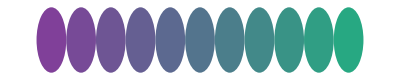

```mathematica
(* TO DO *)
(* start and end color in {red, green, blue} format *)
color0 = {0.5, 0.25, 0.6};
color1 = {0.12, 0.7, 0.5};

(* TO DO *)
(* interpolate color as theta changes. 
 input: color0, color 1 (as global variables) and theta for PolarPlot
  Use globalToLocal function.
 output: color for this position on curve. 
*)
colorInterpolation[theta_] := 
(
	t = globalToLocal[theta];
	color = (1 - t)*(color0) + (t)*(color1)
);

(* TO DO *)
(* create a Table of 11 testColors by calling colorInterpolation *)
delta = paramEnd - paramStart;

testColors = Table[colorInterpolation[delta], {delta, paramStart, paramEnd, (Pi/11)}];

(* TO DO *)
(* Leave these print statements here. Uncomment out when ready to test *)

lgthTestColors = Length[testColors];
Print["Length of testColors = ",lgthTestColors];
Print["color0 = ",color0,"  testColors[[1]] = ",testColors[[1]]];
Print["color1 = ",color1,"  testColors[[last]] = ",testColors[[lgthTestColors]]];


(* TO DO *)
(* create a table of disks and Show them. Tip: Use RGBColor[color] to set the color of a disk to color = {r, g, b} *)

(*circlesPlot = Table[Graphics[{RGBColor[testColors[[i]]], Disk[]}], {i, 1, 11 }];*)
circlesPlot = Table[Graphics[{RGBColor[testColors[[i]]], Disk[{i, 0}, 0.5]}], {i, 1, 11}];
Show[circlesPlot]
```

Part 3 PolarPlot with travelling point that changes color
-- Compete the function pointOnPolar
    You will need to read the Help and understand what PolarPlot does.
-- Fill in the missing code needed for the Manipulate environment to create a moving point that changes color.
   You will use the colorInterpolation function from above.
-- Replace existing curve with your own curve. It must be a function of t and create a fun picture.

```mathematica
(* function for PolarPlot and create graphics plot *)
fct[t_] :=Sin[3t];
polarPlot = PolarPlot[fct[t],{t,paramStart,Pi}];

(* TO DO *)
(* Define a point on the PolarPlot given a parameter value 
   Output: {x,y} *)
pointOnPolar[theta_] := fct[theta]*{Cos[theta], Sin[theta]};

(* TO DO *)
(* Plot the polar plot and a travelling point on the curve *)
Manipulate[ 
color = {0,0,0};
pointPlot = Graphics[{RGBColor[colorInterpolation[theta]],PointSize[0.03],Point[pointOnPolar[theta]]     }];
Show[{polarPlot, pointPlot}],{theta,paramStart, paramEnd}, FrameLabel->{""," ",Style["Color:"Dynamic[NumberForm[color,2]], 20]," "}]
```

Part 4 Surface of Revolution: RevolutionPlot3D
-- Create a plot of revfct over [revDomainStart, revDomainEnd] as defined below
   See the MM tutorial from class for assistance on the MM plotting functions.
-- Complete the function revfct3D that defines the generatrix of the surface of revolution
   You will need to read the Help for RevolutionPlot3D to understand what the {x,y,z} coordinates should be.
-- Create a plot of revfct3D that will appear as a curve of the RevolutionPlot3D surface
    Remove the comments around revfct3Dplot

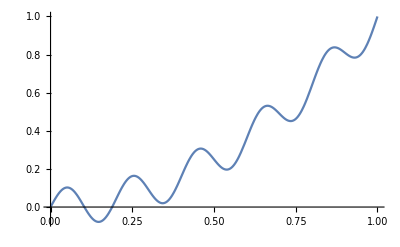

-Graphics3D-

```mathematica
(* domain for revfct *)
revDomainStart = 0.0;
revDomainEnd = 1.0;

(* input function used to create generating curve - generatrix *)
revfct[t_] :=t^2 + Sin[10*Pi*t]*0.1;

(* TO DO *)
(* 2d plot of function statement goes here *)
Plot[revfct[x],{x,revDomainStart,revDomainEnd}]

(* TO DO *)
(* generatrix from revfct *)
revfct3D[s_]  := {0.0, s, revfct[s]};

(* TO DO *)
(* plot generatrix in 3D *)
(* Add PlotStyle->{Red,Thick} *)
revfct3Dplot = ParametricPlot3D[revfct3D[t], {t, revDomainStart, revDomainEnd}, PlotStyle->{Red, Thick}];

(* create surface plot *)
rplot = RevolutionPlot3D[revfct[t],{t,revDomainStart,revDomainEnd}, PlotStyle->Opacity[0.3]];

(* TO DO *)
(* plot surface and curve on surface *)
Show[{revfct3Dplot, rplot},PlotRange->All]
```

Part 5 Spherical Coordinates: SphericalPlot3D
-- Create a plot of sphfct over domain D = [sphDomainStart, sphDomainEnd] as defined
-- Complete the definition of sphfct3D. This is a curve in 3D corresponding to phi=0 and theta in D.
    You will need to read the Help for SphericalPlot3D to learn what this curve definition should be
-- Complete sphfct3Dplot to generate a 3D plot of a curve that appears as a curve on the SphericalPlot3D surface

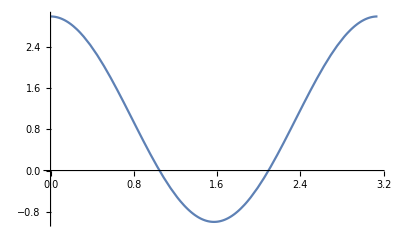

-Graphics3D-

```mathematica
sphDomainStart = 0.0;
sphDomainEnd = Pi;

(* function to use to create generating function *)
sphfct[θ_] :=1+2Cos[2θ];

(* TO DO *)
(* plot the input function *)
Plot[sphfct[t], {t, sphDomainStart, sphDomainEnd}]
 
(* TO DO *)
(* 3d curve for spherical plot surface. Plot curve on surface for phi=0, theta in sphDomain *)
sphfct3D[s_]  := {0, sphfct[s]*Sin[s], sphfct[s]*Cos[s]};

(* TO DO *)
(* create a 3d plot of it *)
(* Add PlotStyle->{Red,Thick} *)
sphfct3Dplot = ParametricPlot3D[sphfct3D[t], {t, sphDomainStart, sphDomainEnd}, PlotStyle->{Red, Thick}];

splot = SphericalPlot3D[sphfct[θ] ,{θ,sphDomainStart ,sphDomainEnd},{ϕ,0,2Pi}, PlotStyle->Opacity[0.3], Mesh->None];

(* plot surface and curve on surface *) 

Show[{sphfct3Dplot,  splot},PlotRange->All]
```